## Функция построения транспортной сети в виде ориентированного графа

```mathematica
Clear[createTransportGraph];
```

```mathematica
createTransportGraph[]:=Module[{n,Oi,Di,intermediates,usedIntermediates,vertices,P={},t={},
tNew,G,addEdge,lenPath,path,paths,extraEdges,u,v,perm},
n=RandomInteger[{1,2}];
Oi=Table["O"<>ToString[i],{i,1,n}];
Di=Table["D"<>ToString[i],{i,1,n}];
intermediates={"A","B","C","E"};
usedIntermediates=RandomSample[intermediates,RandomInteger[{2,Length[intermediates]}]];
vertices=Join[Oi,usedIntermediates,Di];
addEdge[u_,v_]:=Module[{a,b,ti},AppendTo[P,{u,v}];
a=RandomInteger[{-5,5}];While[a==0,a=RandomInteger[{-5,5}]];
b=RandomInteger[{-10,10}];
ti=Function[y,a*y+b];
AppendTo[t,ti];];
Do[lenPath=RandomInteger[{2,4}];
path=RandomSample[usedIntermediates,lenPath-2];
paths=Join[{Oi[[i]]},path,{Di[[i]]}];
Do[addEdge[paths[[j]],paths[[j+1]]],{j,Length[paths]-1}],{i,n}];
extraEdges=RandomInteger[{0,2}];
Do[{u,v}=RandomSample[vertices,2];
If[!MemberQ[P,{u,v}],addEdge[u,v]],{extraEdges}];
perm=RandomSample[vertices];
Do[If[!MemberQ[P,{perm[[i]],perm[[i+1]]}],addEdge[perm[[i]],perm[[i+1]]]],{i,Length[perm]-1}];
tNew=t[[#]][y]&/@Range[Length[t]];
G=Graph[DirectedEdge@@@P,EdgeWeight->tNew,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
<|"Graph"->G,"Vertices"->vertices,"Edges"->P,"CostFunctions"->t|>]
```

## Функция оптимизации транспортного потока

```mathematica
Clear[optimizeTransportFlow]
```

```mathematica
optimizeTransportFlow[graph_,Oγ_,Dγ_,t_,edges_]:=Module[{Ui,checkEd,c,generalflow,X,xα,fi,F},
Ui=Flatten[Table[FindPath[graph,Oγ[[i]],Dγ[[j]],Infinity,All],{i,Length@Oγ},{j,Length@Dγ}],2];
checkEd[e_]:=Table[If[MemberQ[Partition[Ui[[i]],2,1],e],1,0],{i,Length@Ui}];
c=checkEd/@edges;
X=Transpose[Table[Symbol["x"<>ToString[i]],{i,Length@c[[2]]}]];
xα=Table[Sum[c[[i,j]]*X[[j]],{j,Length[X]}],{i,Length[edges]}];
fi=Table[With[{f=t[[i]]},Function[y,Integrate[f[x],{x,0,y}]]],{i,Length[t]}];
F=Total[MapThread[#1[#2]&,{fi,xα}]];
F]
```

## Функция добавления нулевых мостов в транспортную сеть

```mathematica
Clear[addZeroBridges]
```

```mathematica
addZeroBridges[graph_]:=Module[{vertices=graph["Vertices"],P=graph["Edges"],
t=graph["CostFunctions"],intermediates,newP,tα,newG,tNew,bridges,u,v},intermediates=Select[vertices,StringMatchQ[#,LetterCharacter~~___]&&!StringStartsQ[#,"O"]&&!StringStartsQ[#,"D"]&];
newP=P;
tα=t;
bridges={};
Do[u=intermediates[[i]];
v=intermediates[[j]];
If[i<j&&!MemberQ[newP,{u,v}]&&!MemberQ[newP,{v,u}],AppendTo[newP,{u,v}];
AppendTo[tα,Function[y,0]];
AppendTo[bridges,{u,v}]],{i,Length[intermediates]},{j,Length[intermediates]}];
tNew=tα[[#]][y]&/@Range[Length[tα]];
newG=Graph[DirectedEdge@@@newP,EdgeWeight->tNew,EdgeLabels->"EdgeWeight",VertexLabels->"Name",ImageSize->Medium];
<|"Graph"->newG,"Vertices"->vertices,"Edges"->newP,"CostFunctions"->tα,"Bridges"->bridges|>]
```

## Нахождения вектора Вардропа для исходного и преобразованного графов

### Общий поток машин по всей транспортной сети

```mathematica
χ = RandomInteger[{10,20}]
```

12

### Исходный граф - transportGraph1

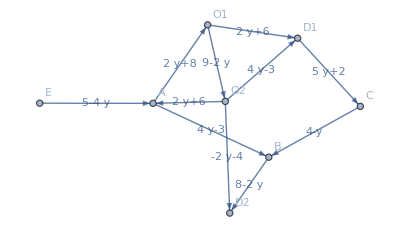

```mathematica
G=createTransportGraph[];
graph1=G["Graph"]
t1=G["CostFunctions"];
edges1=G["Edges"];
```

### Преобразованный граф - transportGraph2

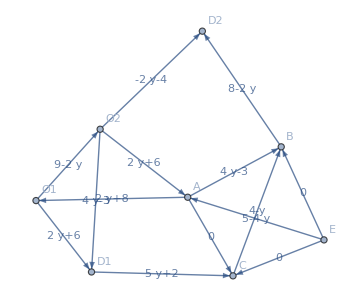

```mathematica
newG=addZeroBridges[G];
graph2=newG["Graph"]
t2=newG["CostFunctions"];
edges2=newG["Edges"];
bridges=newG["Bridges"];
```

### Пункты отправления и назначения графов

```mathematica
Oγ=Select[G["Vertices"],StringStartsQ[#,"O"]&];
Dγ=Select[G["Vertices"],StringStartsQ[#,"D"]&];
```

### Функции оптимизации

```mathematica
F1=optimizeTransportFlow[graph1,Oγ,Dγ,t1,edges1]
F2=optimizeTransportFlow[graph2,Oγ,Dγ,t2,edges2]
```

-3 (x10+x4)+2 (x10+x4)^2+9 (x2+x3+x4+x6)-(x2+x3+x4+x6)^2+6 (x11+x12+x5+x6)+2 (x11+x12+x5+x6)^2+8 (x10+x11+x12+x4+x5+x6)-(x10+x11+x12+x4+x5+x6)^2-3 (x11+x2+x6+x7)+2 (x11+x2+x6+x7)^2+8 (x12+x8)+(x12+x8)^2+6 (x10+x12+x4+x8)+(x10+x12+x4+x8)^2+6 (x1+x12+x5+x8)+(x1+x12+x5+x8)^2-4 (x3+x9)-(x3+x9)^2

-4 (x10+x3)-(x10+x3)^2-3 (x11+x4)+2 (x11+x4)^2+2 (x12+x14+x5+x6)+5/2 (x12+x14+x5+x6)^2+9 (x2+x3+x4+x6+x7)-(x2+x3+x4+x6+x7)^2+4 (x12+x13+x14+x5+x6+x7)-1/2 (x12+x13+x14+x5+x6+x7)^2+8 (x11+x12+x13+x14+x4+x5+x6+x7)-(x11+x12+x13+x14+x4+x5+x6+x7)^2-3 (x12+x2+x6+x8)+2 (x12+x2+x6+x8)^2+8 (x14+x9)+(x14+x9)^2+6 (x1+x14+x5+x9)+(x1+x14+x5+x9)^2+6 (x11+x13+x14+x4+x7+x9)+(x11+x13+x14+x4+x7+x9)^2

### Необходимые данные для нахождения вектора Вардропа двух графов

```mathematica
Uβ1=Flatten[Table[FindPath[graph1,Oγ[[i]],Dγ[[j]],Infinity,All],{i,Length@Oγ},{j,Length@Dγ}],2];
Uβ2=Flatten[Table[FindPath[graph2,Oγ[[i]],Dγ[[j]],Infinity,All],{i,Length@Oγ},{j,Length@Dγ}],2];
checkEd1[e_]:=Table[If[MemberQ[Partition[Uβ1[[i]],2,1],e],1,0],{i,Length@Uβ1}]
checkEd2[e_]:=Table[If[MemberQ[Partition[Uβ2[[i]],2,1],e],1,0],{i,Length@Uβ2}]
c1=checkEd1/@edges1;
c2=checkEd2/@edges2;
X1 =Transpose[Table[Symbol["x"<>ToString[i]],{i,Length@c1[[2]]}]];
X2 =Transpose[Table[Symbol["x"<>ToString[i]],{i,Length@c2[[2]]}]];
```

### Условия существования вектора Вардропа

```mathematica
flowСondition1=Total[X1]== χ;
flowCondition2=Total[X2]==χ;
nonnegativityСondition1=And@@Thread[X1>=0];
nonnegativityСondition2=And@@Thread[X2>=0];
integerСondition1 = Element[X1,Integers];
integerСondition2 = Element[X2,Integers];
```

### Минимизируем функцию оптимизации

```mathematica
If[FindInstance[flowСondition1&&nonnegativityСondition1&&integerСondition1,X1,Integers]=!={},
minNM1=NMinimize[{F1,flowСondition1&&nonnegativityСondition1&&integerСondition1},X1],Print["Решений нет!"];
minNM1=$Failed];
If[!FreeQ[minNM1,Indeterminate]||!FreeQ[minNM1,ComplexInfinity],Print["Оптимизация не удалась: нет допустимых решений"];
minNM1=$Failed];
timingNM1 = minNM1//AbsoluteTiming
If[FindInstance[flowCondition2&&nonnegativityСondition2&&integerСondition2,X2,Integers]=!={},
minNM2=NMinimize[{F2,flowCondition2&&nonnegativityСondition2&&integerСondition2},X2],Print["Решений нет!"];
minNM2=$Failed];
If[!FreeQ[minNM2,Indeterminate]||!FreeQ[minNM2,ComplexInfinity],Print["Оптимизация не удалась: нет допустимых решений"];
minNM2=$Failed];
timingNM2 = minNM2//AbsoluteTiming
```

{3.×10^-7,{-228.,{x1→0,x2→0,x3→12,x4→0,x5→0,x6→0,x7→0,x8→0,x9→0,x10→0,x11→0,x12→0}}}

{3.×10^-7,{-228.,{x1→0,x2→0,x3→12,x4→0,x5→0,x6→0,x7→0,x8→0,x9→0,x10→0,x11→0,x12→0,x13→0,x14→0}}}

## Сравнение результатов

```mathematica
bridgesString=StringJoin[Riffle[ToString/@bridges,", "]];
Row[{Labeled[graph1,"До добавления мостов"],Spacer[20],Labeled[graph2,"После добавления мостов "<>bridgesString<>""]}]
```

-Graphics-До добавления мостов-Graphics-После добавления мостов {E, C}, {E, B}, {A, C}

```mathematica
CompareFlowEfficiency[minNM1_,minNM2_]:=Module[{val1,val2,hasSolution1,hasSolution2},
hasSolution1=!MatchQ[minNM1,$Failed|{_,{__Indeterminate}}|{_,{_DirectedInfinity,__}}];
hasSolution2=!MatchQ[minNM2,$Failed|{_,{__Indeterminate}}|{_,{_DirectedInfinity,__}}];
Which[!hasSolution1&&!hasSolution2,Print["Оба варианта транспортной системы не имеют допустимых распределений потока."],
hasSolution1&&!hasSolution2,Print["Добавление моста привело к недопустимому распределению потока."],
!hasSolution1&&hasSolution2,Print["Добавление моста разрешило проблему недопустимого распределения в исходной системе."],
hasSolution1&&hasSolution2,val1=minNM1[[1]];
val2=minNM2[[1]];
If[Abs[val1-val2]<10^-6,Print["Добавление моста не изменило общие транспортные затраты (разница < 10^-6)."],If[val2<val1,Print[StringForm["Добавление моста снизило транспортные затраты с `` до `` Экономия составляет ``.",val1,val2,val1-val2]],Print[StringForm["Добавление моста увеличило транспортные затраты с `` до `` Потери составляют ``.",val1,val2,val2-val1]]]],True,Print["Невозможно сравнить решения."]]];
CompareFlowEfficiency[minNM1,minNM2]
```

Добавление моста не изменило общие транспортные затраты (разница < 10^-6).